```mathematica
(*****************************************************************************************************************
1. add NETLink
  *it should be loaded from the package in the Mathematica directory;
   C:\Program Files\Wolfram Research\Mathematica\7.0\SystemFiles\Links\NETLink.
   However, it is only compatable with.NET framework 3.5.
   Therefore, I customized it in Library/NETLink (for Mathematica).
   So, add the library in the project.
2. project property :
   Debug tab :
	*start action -> start external program
	   D:\htnarobot_svn\VisualStudioSolutions\Library\NETLink (for Mathematica)\bin\Debug\InstallableNET.exe
	*start option -> command line argument
	   -linkmode listen -linkname foo
3. run project in the debugging mode
4. open "debug test.nb" in mathematica
and run it.
*****************************************************************************************************************)
```

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["NETLink`","..\\..\\Library\\NETLink (for Mathematica)\\bin\\Debug\\NETLink.m"];
InstallNET[LinkConnect["elaest"]];
LoadNETAssembly[".\\LinearElasticityEstimator.dll"];
```

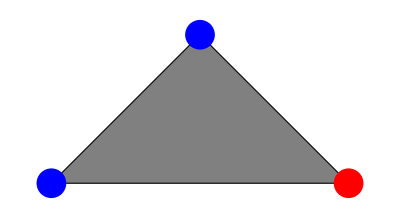
```mathematica
-Graphics-;
{nodes,triags,boundaries,Forces,plotrange} = Module[{nodes,triags,boundaries,Forces,plotrange},
	nodes = {{0.,0.},{2.,0.},{1.,1.}};
	triags = {{1,2,3}};
	boundaries = {{1,{1,2}}};
	boundaries = {{1,{1,2}},{3,{1,2}}};
	Forces[FF_] := {{2,{FF,FF}}};
	plotrange = {{-1,7},{-4,4}};
	{nodes,triags,boundaries,Forces,plotrange}
];
```

```mathematica
obj = NETNew["HTLib.Mathematica.MathBridge"];
(* Test Simulation *)
Module[{thick=0.5, EE = 1.0, vv = 0.2},
	obj@Simulate[nodes,triags,thick,EE,vv,{1},2,{0.0,-1.0}]
];

Draw[nodes_,triags_,forces_,boundaries_,plotrange_,optional_:{}]:=Module[{},
	(* optional = {Text[Style["test",Large],{-0.5,0.5},Background->LightRed]}} *)
	Graphics[{{}
		,{FaceForm[Gray(*Transparent*)],EdgeForm[{Thick,Black}],Table[Polygon[Table[nodes[[i]],{i,triags[[f]]}]],{f,Length[triags]}]}
		,Table[{Blue,Opacity[1],Disk[nodes[[boundary]],0.1]},{boundary,boundaries}]
		,Table[{Red,Opacity[1],Disk[nodes[[force[[1]]]],0.1]},{force,forces}]
		,optional
		}
		,AxesStyle->Directive[Orange,Opacity[1],12]
		,Axes->True
		,PlotRange->plotrange
	]
];

PlotSimulation[thick_,E_,v_,boundaryid_,forceid_,forcevalues_,plotrange_]:=Module[{Q, n, dnodes, nnodes, debug},
	n = Length[nodes];
	dnodes = obj@Simulate[nodes,triags,thick,E,v,boundaryid,forceid,forcevalues];
	nnodes = nodes + dnodes;
	Draw[nnodes,triags,{{forceid,forcevalues}},boundaryid, plotrange
	,{Text[Style[nnodes[[2]],Medium],{0,2},{-1,1},Background->LightGray]}]
];

Module[{},(*FF,EE,thick,vv},*)
	Animate[PlotSimulation[thick,EE,vv,{1,3},2,{FF,FF},plotrange]
		,{{FF,0.0},-0.5,0.5},{{thick,0.5},0.01,10},{{EE,1.0},0.00000001,10},{{vv,0.2},0,0.49999999}
		,AnimationRunning->False]
]
```

```mathematica
estimator = obj@BuildEstimator[nodes,triags,0.5];
obj@EstimatorInit[estimator,{1,3},2,1000];
obj@EstimatorIterate[estimator,{1.0,1},{1,1}];
```